```mathematica
dx=0.01;
n=1/dx^2;
f[x_]:=x-Floor[x/dx]dx;
g[x_]:=dx/2-dx/π∑_(k=1)^n Sin[(2π k x)/dx]/k
```

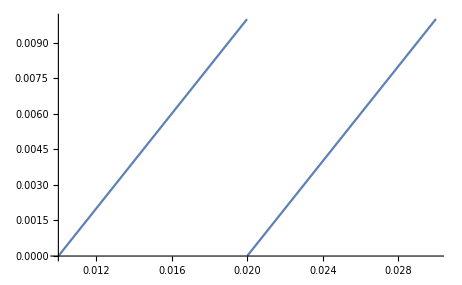

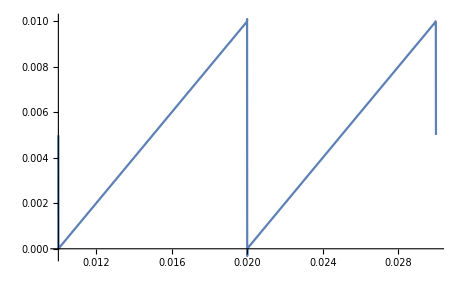

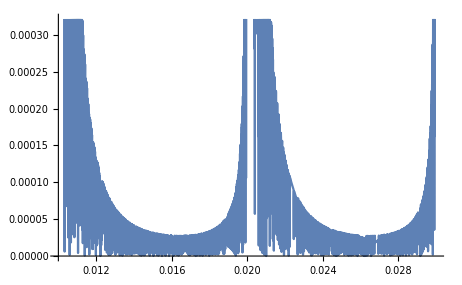

```mathematica
Plot[f[x],{x,dx,3 dx}]
Plot[g[x],{x,dx,3 dx}]
Plot[Abs[g[x]-f[x]]/f[x],{x,dx,3 dx}]
```

```mathematica
Φ[x_,y_]=-1/(√(x^2+y^2));
ForceDiscrete[x_,y_]:=-{(Φ[Floor[x+1],Floor[y]]-Φ[Floor[x],Floor[y]])(1-(y-Floor[y]))+(y-Floor[y])(Φ[Floor[x+1],Floor[y+1]]-Φ[Floor[x],Floor[y+1]]),(Φ[Floor[x],Floor[y+1]]-Φ[Floor[x],Floor[y]])(1-(x-Floor[x]))+(x-Floor[x]) (Φ[Floor[x+1],Floor[y+1]]-Φ[Floor[x+1],Floor[y]])};
```

```mathematica
RealForce[x,y]:={D[Φ[x,y],x],D[Φ[x,y],y]}
```

```mathematica
RealForce[x,y]
```

{x/((x^2+y^2)^(3/2)),y/((x^2+y^2)^(3/2))}

```mathematica
RealForce[x,y]/.{x->1,y->1}
```

{1/(2 √2),1/(2 √2)}

```mathematica
(*ForceDiscrete[x,y]-RealForce[x,y]*)
```

```mathematica
(ForceDiscrete[x,y]-RealForce[x,y])/RealForce[x,y];a=10;
```

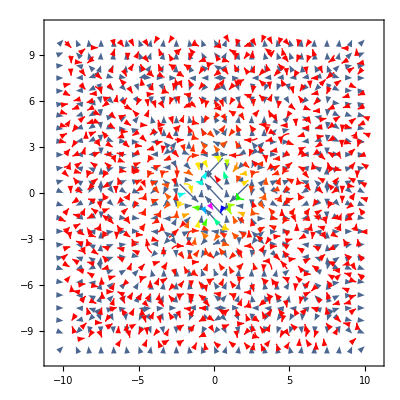

```mathematica
VectorPlot[(ForceDiscrete[x,y]+{x/((x^2+y^2)^(3/2)),y/((x^2+y^2)^(3/2))}),{x,a,-a},{y,a,-a},
StreamPoints->Fine,PerformanceGoal->"Quality",StreamColorFunction->Hue,VectorPoints->Fine,VectorScale->Small]
```